```mathematica
SetDirectory@NotebookDirectory[]
```

/Users/leima/github/neuphysics/codebase/mma/dispersion-relation

## Solving Multiangle Problem Using Polarization Tensor

```mathematica
eta=DiagonalMatrix[{1,-1,-1,-1}];

angleRange={Pi/3,5Pi/6};
```

I assume the beams are the same for different directions

```mathematica
Integrate[
Cos[x]DiracDelta[x-ArcCos@0.9],
{x,0,1}]
```

0.9

```mathematica
(*gDist[g0_,theta_,phi_]:=g0 Piecewise[
{
{1,0≤theta≤Pi/2},
{-1,Pi/2<theta≤Pi}
}
]*)
(*gDist[g0_,theta_,phi_]:=g0 DiracDelta[theta-ArcCos@0.9]+g0 DiracDelta[theta-ArcCos@0.3]*)
```

```mathematica
kno[nIndex_,theta_,phi_]:={1,nIndex Cos[phi]Sin[theta],nIndex Sin[phi]Sin[theta],nIndex Cos[theta]}
k[omega_,nIndex_,theta_,phi_]:=omega kno[nIndex,theta,phi]
```

```mathematica
v[theta_,phi_]:={1,Cos[phi]Sin[theta],Sin[phi]Sin[theta],Cos[theta]}

vvMatrix[theta_,phi_]=Outer[Times,v[theta,phi],v[theta,phi]];
%//MatrixForm
```

(1 | Cos[phi] Sin[theta] | Sin[phi] Sin[theta] | Cos[theta]
Cos[phi] Sin[theta] | Cos[phi]^2 Sin[theta]^2 | Cos[phi] Sin[phi] Sin[theta]^2 | Cos[phi] Cos[theta] Sin[theta]
Sin[phi] Sin[theta] | Cos[phi] Sin[phi] Sin[theta]^2 | Sin[phi]^2 Sin[theta]^2 | Cos[theta] Sin[phi] Sin[theta]
Cos[theta] | Cos[phi] Cos[theta] Sin[theta] | Cos[theta] Sin[phi] Sin[theta] | Cos[theta]^2)

```mathematica
kno[nIndex,theta,phi].v[theta,phi]
```

1+nIndex Cos[theta]^2+nIndex Cos[phi]^2 Sin[theta]^2+nIndex Sin[phi]^2 Sin[theta]^2

Polarization Tensor Method

```mathematica
polTensor1=eta+1/omega Integrate[
gDist[1,theta,phi] vvMatrix[theta,phi]/(kno[nIndex,theta,phi].v[theta,phi]),
{theta,0,Pi},{phi,0,2Pi}]
```

{{1+(4 π)/((1+nIndex) omega),0,0,7.53982/((1+nIndex) omega)},{0,-1+3.45575/((1+nIndex) omega),0,0},{0,0,-1+3.45575/((1+nIndex) omega),0},{7.53982/((1+nIndex) omega),0,0,-1+5.65487/((1+nIndex) omega)}}

```mathematica
timeDep[nIndex_]=omega/.Solve[Det@polTensor1==0,omega]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{-6.28319/nIndex,-5.29614/nIndex,-0.987049/nIndex,12.5664/nIndex}

```mathematica
dataPlt=Table[
{First@timeDep[n],n First@timeDep[n]},
{n,-4,4,0.09}]
```

{{1.5708,-6.28319},{1.60695,-6.28319},{1.64481,-6.28319},{1.6845,-6.28319},{1.72615,-6.28319},{1.76991,-6.28319},{1.81595,-6.28319},{1.86445,-6.28319},{1.91561,-6.28319},{1.96965,-6.28319},{2.02683,-6.28319},{2.08744,-6.28319},{2.15178,-6.28319},{2.22021,-6.28319},{2.29313,-6.28319},{2.37101,-6.28319},{2.45437,-6.28319},{2.5438,-6.28319},{2.63999,-6.28319},{2.74375,-6.28319},{2.85599,-6.28319},{2.97781,-6.28319},{3.11049,-6.28319},{3.25554,-6.28319},{3.41477,-6.28319},{3.59039,-6.28319},{3.78505,-6.28319},{4.00203,-6.28319},{4.2454,-6.28319},{4.52028,-6.28319},{4.83322,-6.28319},{5.19272,-6.28319},{5.60999,-6.28319},{6.10018,-6.28319},{6.68424,-6.28319},{7.39198,-6.28319},{8.26735,-6.28319},{9.37789,-6.28319},{10.8331,-6.28319},{12.8228,-6.28319},{15.708,-6.28319},{20.2683,-6.28319},{28.5599,-6.28319},{48.3322,-6.28319},{157.08,-6.28319},{-125.664,-6.28319},{-44.8799,-6.28319},{-27.3182,-6.28319},{-19.635,-6.28319},{-15.3248,-6.28319},{-12.5664,-6.28319},{-10.6495,-6.28319},{-9.23998,-6.28319},{-8.15998,-6.28319},{-7.30603,-6.28319},{-6.61388,-6.28319},{-6.04152,-6.28319},{-5.56034,-6.28319},{-5.15015,-6.28319},{-4.79632,-6.28319},{-4.48799,-6.28319},{-4.2169,-6.28319},{-3.9767,-6.28319},{-3.76239,-6.28319},{-3.56999,-6.28319},{-3.39632,-6.28319},{-3.23876,-6.28319},{-3.09517,-6.28319},{-2.96377,-6.28319},{-2.84307,-6.28319},{-2.73182,-6.28319},{-2.62895,-6.28319},{-2.53354,-6.28319},{-2.44482,-6.28319},{-2.3621,-6.28319},{-2.28479,-6.28319},{-2.21239,-6.28319},{-2.14443,-6.28319},{-2.08052,-6.28319},{-2.02032,-6.28319},{-1.9635,-6.28319},{-1.90978,-6.28319},{-1.85893,-6.28319},{-1.81072,-6.28319},{-1.76494,-6.28319},{-1.72142,-6.28319},{-1.68,-6.28319},{-1.64052,-6.28319},{-1.60285,-6.28319}}

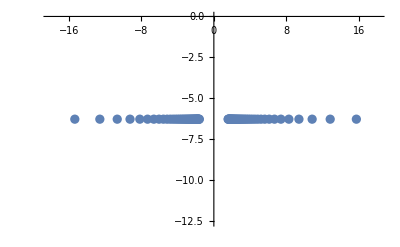

```mathematica
ListPlot[dataPlt]
```

Polarization (More Efficient) for 2 Beams

```mathematica
vvMatrix[theta,phi]/(kno[nIndex,thetaK,phiK].eta.v[theta,phi])//MatrixForm
```

(1/(1-nIndex Cos[theta] Cos[thetaK]-nIndex Cos[phi] Cos[phiK] Sin[theta] Sin[thetaK]-nIndex Sin[phi] Sin[phiK] Sin[theta] Sin[thetaK]) | (Cos[phi] Sin[theta])/(1-nIndex Cos[theta] Cos[thetaK]-nIndex Cos[phi] Cos[phiK] Sin[theta] Sin[thetaK]-nIndex Sin[phi] Sin[phiK] Sin[theta] Sin[thetaK]) | (Sin[phi] Sin[theta])/(1-nIndex Cos[theta] Cos[thetaK]-nIndex Cos[phi] Cos[phiK] Sin[theta] Sin[thetaK]-nIndex Sin[phi] Sin[phiK] Sin[theta] Sin[thetaK]) | Cos[theta]/(1-nIndex Cos[theta] Cos[thetaK]-nIndex Cos[phi] Cos[phiK] Sin[theta] Sin[thetaK]-nIndex Sin[phi] Sin[phiK] Sin[theta] Sin[thetaK])
(Cos[phi] Sin[theta])/(1-nIndex Cos[theta] Cos[thetaK]-nIndex Cos[phi] Cos[phiK] Sin[theta] Sin[thetaK]-nIndex Sin[phi] Sin[phiK] Sin[theta] Sin[thetaK]) | (Cos[phi]^2 Sin[theta]^2)/(1-nIndex Cos[theta] Cos[thetaK]-nIndex Cos[phi] Cos[phiK] Sin[theta] Sin[thetaK]-nIndex Sin[phi] Sin[phiK] Sin[theta] Sin[thetaK]) | (Cos[phi] Sin[phi] Sin[theta]^2)/(1-nIndex Cos[theta] Cos[thetaK]-nIndex Cos[phi] Cos[phiK] Sin[theta] Sin[thetaK]-nIndex Sin[phi] Sin[phiK] Sin[theta] Sin[thetaK]) | (Cos[phi] Cos[theta] Sin[theta])/(1-nIndex Cos[theta] Cos[thetaK]-nIndex Cos[phi] Cos[phiK] Sin[theta] Sin[thetaK]-nIndex Sin[phi] Sin[phiK] Sin[theta] Sin[thetaK])
(Sin[phi] Sin[theta])/(1-nIndex Cos[theta] Cos[thetaK]-nIndex Cos[phi] Cos[phiK] Sin[theta] Sin[thetaK]-nIndex Sin[phi] Sin[phiK] Sin[theta] Sin[thetaK]) | (Cos[phi] Sin[phi] Sin[theta]^2)/(1-nIndex Cos[theta] Cos[thetaK]-nIndex Cos[phi] Cos[phiK] Sin[theta] Sin[thetaK]-nIndex Sin[phi] Sin[phiK] Sin[theta] Sin[thetaK]) | (Sin[phi]^2 Sin[theta]^2)/(1-nIndex Cos[theta] Cos[thetaK]-nIndex Cos[phi] Cos[phiK] Sin[theta] Sin[thetaK]-nIndex Sin[phi] Sin[phiK] Sin[theta] Sin[thetaK]) | (Cos[theta] Sin[phi] Sin[theta])/(1-nIndex Cos[theta] Cos[thetaK]-nIndex Cos[phi] Cos[phiK] Sin[theta] Sin[thetaK]-nIndex Sin[phi] Sin[phiK] Sin[theta] Sin[thetaK])
Cos[theta]/(1-nIndex Cos[theta] Cos[thetaK]-nIndex Cos[phi] Cos[phiK] Sin[theta] Sin[thetaK]-nIndex Sin[phi] Sin[phiK] Sin[theta] Sin[thetaK]) | (Cos[phi] Cos[theta] Sin[theta])/(1-nIndex Cos[theta] Cos[thetaK]-nIndex Cos[phi] Cos[phiK] Sin[theta] Sin[thetaK]-nIndex Sin[phi] Sin[phiK] Sin[theta] Sin[thetaK]) | (Cos[theta] Sin[phi] Sin[theta])/(1-nIndex Cos[theta] Cos[thetaK]-nIndex Cos[phi] Cos[phiK] Sin[theta] Sin[thetaK]-nIndex Sin[phi] Sin[phiK] Sin[theta] Sin[thetaK]) | Cos[theta]^2/(1-nIndex Cos[theta] Cos[thetaK]-nIndex Cos[phi] Cos[phiK] Sin[theta] Sin[thetaK]-nIndex Sin[phi] Sin[phiK] Sin[theta] Sin[thetaK]))

```mathematica
nMatIntPhi[theta_,nIndex_,thetaK_:0,phiK_:0]:=Module[{thetaM,phiKM,thetaKM},

thetaM=theta;
phiKM=phiK;
thetaKM=thetaK;

Assuming[nIndex∈Reals && (-1<n<0||0<n<1),
Integrate[
vvMatrix[thetaM,phi]/(kno[nIndex,thetaKM,phiKM].eta.v[thetaM,phi]),
{phi,0,2Pi}]
]
];
```

```mathematica
nMatIntPhi0[theta_,n_]=nMatIntPhi[theta,n,0,0]
```

{{(2 π)/(1-n Cos[theta]),0,0,(2 π Cos[theta])/(1-n Cos[theta])},{0,(π Sin[theta]^2)/(1-n Cos[theta]),0,0},{0,0,(π Sin[theta]^2)/(1-n Cos[theta]),0},{(2 π Cos[theta])/(1-n Cos[theta]),0,0,(2 π Cos[theta]^2)/(1-n Cos[theta])}}

```mathematica
nMatIntPhi0[theta,n]//MatrixForm
```

((2 π)/(1-n Cos[theta]) | 0 | 0 | (2 π Cos[theta])/(1-n Cos[theta])
0 | (π Sin[theta]^2)/(1-n Cos[theta]) | 0 | 0
0 | 0 | (π Sin[theta]^2)/(1-n Cos[theta]) | 0
(2 π Cos[theta])/(1-n Cos[theta]) | 0 | 0 | (2 π Cos[theta]^2)/(1-n Cos[theta]))

```mathematica
omegaFun[g1_,g2_,nIndex_,theta1_,theta2_]=omega/.Solve[Det[
omega eta+(g1 nMatIntPhi0[theta1,nIndex]Sin[theta1]+g2 nMatIntPhi0[theta2,nIndex]Sin[theta2])
]==0,
omega]
```

{(g1 π Sin[theta1]^3-g1 nIndex π Cos[theta2] Sin[theta1]^3+g2 π Sin[theta2]^3-g2 nIndex π Cos[theta1] Sin[theta2]^3)/((-1+nIndex Cos[theta1]) (-1+nIndex Cos[theta2])),(g1 π Sin[theta1]^3-g1 nIndex π Cos[theta2] Sin[theta1]^3+g2 π Sin[theta2]^3-g2 nIndex π Cos[theta1] Sin[theta2]^3)/((-1+nIndex Cos[theta1]) (-1+nIndex Cos[theta2])),(-2 g1 π Sin[theta1]+2 g1 π Cos[theta1]^2 Sin[theta1]+2 g1 nIndex π Cos[theta2] Sin[theta1]-2 g1 nIndex π Cos[theta1]^2 Cos[theta2] Sin[theta1]-2 g2 π Sin[theta2]+2 g2 nIndex π Cos[theta1] Sin[theta2]+2 g2 π Cos[theta2]^2 Sin[theta2]-2 g2 nIndex π Cos[theta1] Cos[theta2]^2 Sin[theta2]-√((2 g1 π Sin[theta1]-2 g1 π Cos[theta1]^2 Sin[theta1]-2 g1 nIndex π Cos[theta2] Sin[theta1]+2 g1 nIndex π Cos[theta1]^2 Cos[theta2] Sin[theta1]+2 g2 π Sin[theta2]-2 g2 nIndex π Cos[theta1] Sin[theta2]-2 g2 π Cos[theta2]^2 Sin[theta2]+2 g2 nIndex π Cos[theta1] Cos[theta2]^2 Sin[theta2])^2-4 (1-nIndex Cos[theta1]-nIndex Cos[theta2]+nIndex^2 Cos[theta1] Cos[theta2]) (-4 g1 g2 π^2 Cos[theta1]^2 Sin[theta1] Sin[theta2]+8 g1 g2 π^2 Cos[theta1] Cos[theta2] Sin[theta1] Sin[theta2]-4 g1 g2 π^2 Cos[theta2]^2 Sin[theta1] Sin[theta2])))/(2 (1-nIndex Cos[theta1]-nIndex Cos[theta2]+nIndex^2 Cos[theta1] Cos[theta2])),(-2 g1 π Sin[theta1]+2 g1 π Cos[theta1]^2 Sin[theta1]+2 g1 nIndex π Cos[theta2] Sin[theta1]-2 g1 nIndex π Cos[theta1]^2 Cos[theta2] Sin[theta1]-2 g2 π Sin[theta2]+2 g2 nIndex π Cos[theta1] Sin[theta2]+2 g2 π Cos[theta2]^2 Sin[theta2]-2 g2 nIndex π Cos[theta1] Cos[theta2]^2 Sin[theta2]+√((2 g1 π Sin[theta1]-2 g1 π Cos[theta1]^2 Sin[theta1]-2 g1 nIndex π Cos[theta2] Sin[theta1]+2 g1 nIndex π Cos[theta1]^2 Cos[theta2] Sin[theta1]+2 g2 π Sin[theta2]-2 g2 nIndex π Cos[theta1] Sin[theta2]-2 g2 π Cos[theta2]^2 Sin[theta2]+2 g2 nIndex π Cos[theta1] Cos[theta2]^2 Sin[theta2])^2-4 (1-nIndex Cos[theta1]-nIndex Cos[theta2]+nIndex^2 Cos[theta1] Cos[theta2]) (-4 g1 g2 π^2 Cos[theta1]^2 Sin[theta1] Sin[theta2]+8 g1 g2 π^2 Cos[theta1] Cos[theta2] Sin[theta1] Sin[theta2]-4 g1 g2 π^2 Cos[theta2]^2 Sin[theta1] Sin[theta2])))/(2 (1-nIndex Cos[theta1]-nIndex Cos[theta2]+nIndex^2 Cos[theta1] Cos[theta2]))}

## Plots

```mathematica
dataPltTwoBeamPlt[g1_,g2_,n_,theta1_,theta2_,numrange_:{-8.9,8.9},numstep_:0.009,pltRange_:{{-5,5},{-5,5}}]:=Module[{pltDataM},

pltDataM=Table[
Table[
{n,1}omegaFun[g1,g2,n,theta1,theta2][[i]],
{n,numrange[[1]],numrange[[2]],numstep}],
{i,1,4}];

ListPlot[pltDataM,Joined->False,Frame->True,ImageSize->Large,PlotRange->pltRange,FrameLabel->{"k","omega"}]
];
```

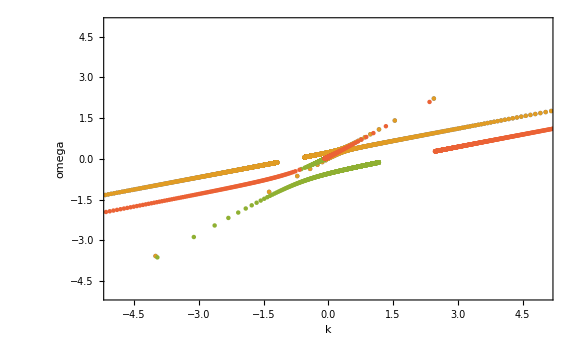

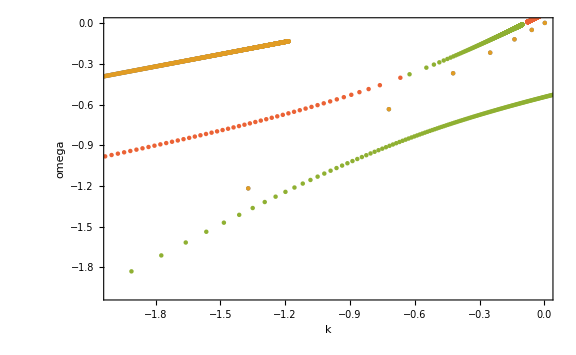

```mathematica
dataPltTwoBeamPlt[0.5/(2Pi),0.5/(2Pi),n,ArcCos@0.9,ArcCos@0.3,{-8.9,8.9}]
dataPltTwoBeamPlt[0.5/(2Pi),0.5/(2Pi),n,ArcCos@0.9,ArcCos@0.3,{-8.9,8.9},0.009,{{-2,0},{-2,0}}]//Quiet
```

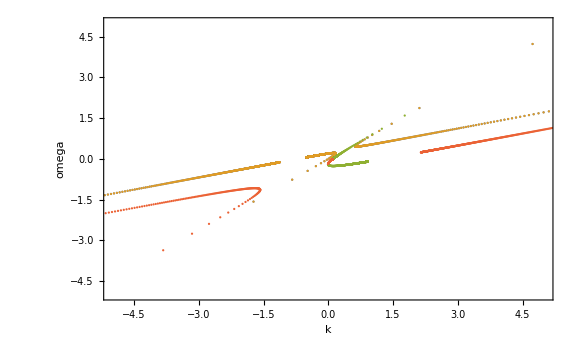

```mathematica
dataPltTwoBeamPlt[-0.5/(2Pi),0.5/(2Pi),n,ArcCos@0.9,ArcCos@0.3]
```

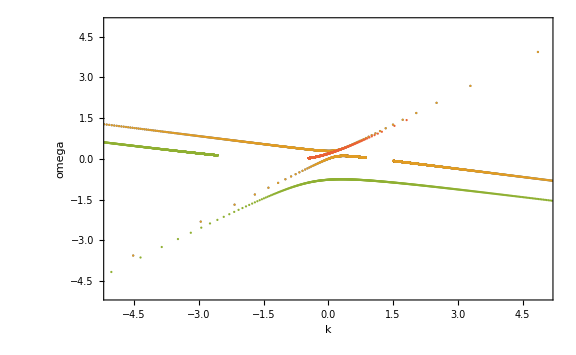

```mathematica
dataPltTwoBeamPlt[0.5/(2Pi),0.5/(2Pi),n,ArcCos@0.8,ArcCos[-0.2],{-19.9,19.9},0.009,{{-5,5},{-5,5}}]//Quiet
```

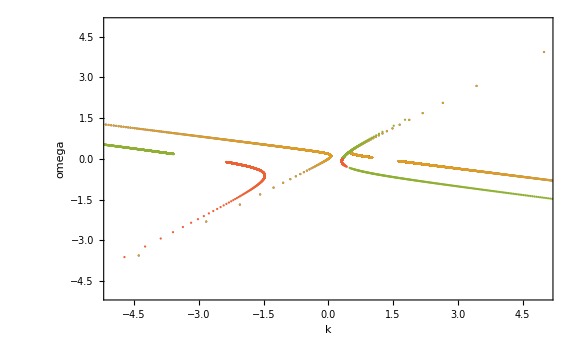

```mathematica
dataPltTwoBeamPlt[-0.5/(2Pi),0.5/(2Pi),n,ArcCos@0.8,ArcCos[-0.2],{-19.9,19.9}]//Quiet
```

Numerically Solve it

## Three Beams

```mathematica
omegaFun3[g1_,g2_,g3_,nIndex_,theta1_,theta2_,theta3_]=Module[{theta1M,theta2M,theta3M,theta4M},
theta1M=theta1;
theta2M=theta2;
theta3M=theta3;



omega/.Solve[Det[
omega eta+(g1 nMatIntPhi0[theta1,nIndex]Sin[theta1]+g2 nMatIntPhi0[theta2,nIndex]Sin[theta2]+g3 nMatIntPhi0[theta3,nIndex]Sin[theta3])
]==0,
omega]
];
```

```mathematica
omegaFun3[1,1,-1,nIndex,Pi/5,2Pi/5,Pi/2+2Pi/5];
```

```mathematica
dataPlt3BeamPlt[g1_,g2_,g3_,n_,theta1_,theta2_,theta3_,numrange_:{-8.9,8.9},numstep_:0.09,pltRange_:{{-5,5},{-5,5}}]:=Module[{pltDataM},

pltDataM=Table[
Table[
{n,1}omegaFun3[g1,g2,g3,n,theta1,theta2,theta3][[i]],
{n,numrange[[1]],numrange[[2]],numstep}],
{i,1,4}];

ListPlot[pltDataM,Joined->False,Frame->True,ImageSize->Large,PlotRange->pltRange,FrameLabel->{"k","omega"}]
];
```

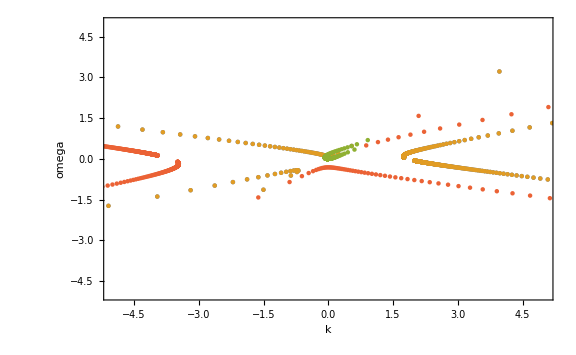

```mathematica
dataPlt3BeamPlt[0.5/(2Pi),-0.5/(2Pi),0.5/(2Pi),n,ArcCos@0.8,ArcCos@0.3,ArcCos[-0.2],{-30.9,30.9},0.09,{{-5,5},{-5,5}}]
```

## Four Beams

It turns out that analytically solving four beams is toooooo slow. I changed it to numerical method.

Also I found the corresponding eigenvalue problem. maybe Mathematica is good at finding eigenvalues so I try that.

```mathematica
nMatFun4[g1_,g2_,g3_,g4_,nIndex_,theta1_,theta2_,theta3_,theta4_]=Module[{theta1M,theta2M,theta3M,theta4M,nMatM},
theta1M=theta1;
theta2M=theta2;
theta3M=theta3;
theta4M=theta4;


nMatM=(g1 nMatIntPhi0[theta1,nIndex]Sin[theta1]+g2 nMatIntPhi0[theta2,nIndex]Sin[theta2]+g3 nMatIntPhi0[theta3,nIndex]Sin[theta3]+g4 nMatIntPhi0[theta4,nIndex]Sin[theta4]);



nMatM[[1]]=-nMatM[[1]];

nMatM

];
```

```mathematica
(* A Timing calculates that the following function requires almost 80sec to finish. *)
omegaFun4[g1_,g2_,g3_,g4_,nIndex_,theta1_,theta2_,theta3_,theta4_]=Eigenvalues@nMatFun4[g1,g2,g3,g4,nIndex,theta1,theta2,theta3,theta4]
```

{(g1 π Sin[theta1]^3)/(1-nIndex Cos[theta1])+(g2 π Sin[theta2]^3)/(1-nIndex Cos[theta2])+(g3 π Sin[theta3]^3)/(1-nIndex Cos[theta3])+(g4 π Sin[theta4]^3)/(1-nIndex Cos[theta4]),(g1 π 1^3)/(1-1)+1+1+1,1,(π (1))/(2 3 (-1+nIndex Cos[theta4]))}
 |  |  |  |

```mathematica
omegaFun4[g1,g2,g3,g4,nIndex,theta1,theta2,theta3,theta4]
```

{(g1 π Sin[theta1]^3)/(1-nIndex Cos[theta1])+(g2 π Sin[theta2]^3)/(1-nIndex Cos[theta2])+(g3 π Sin[theta3]^3)/(1-nIndex Cos[theta3])+(g4 π Sin[theta4]^3)/(1-nIndex Cos[theta4]),(g1 π 1^3)/(1-1)+1+1+1,1,(π (1))/(2 3 (-1+nIndex Cos[theta4]))}
 |  |  |  |

```mathematica
dataPlt4BeamPlt[g1_,g2_,g3_,g4_,theta1_,theta2_,theta3_,theta4_,numrange_:{-8.9,8.9},numstep_:0.09,pltRange_:{{-5,5},{-5,5}}]:=Module[{pltDataM},

pltDataM=Table[
Table[
{n,1}omegaFun4[g1,g2,g3,g4,n,theta1,theta2,theta3,theta4][[i]],
{n,numrange[[1]],numrange[[2]],numstep}],
{i,1,4}];

ListPlot[pltDataM,Joined->False,Frame->True,ImageSize->Large,PlotRange->pltRange,FrameLabel->{"k","omega"}]
];
```

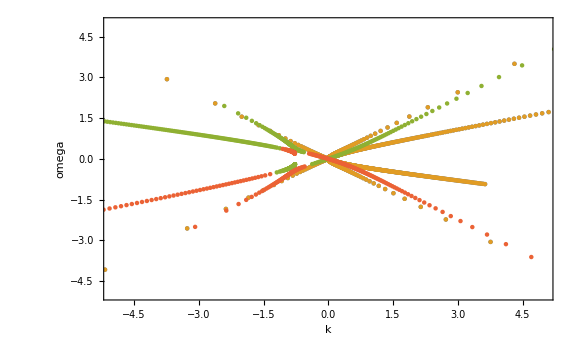

```mathematica
dataPlt4BeamPlt[0.5/(2Pi),0.5/(2Pi),-0.5/(2Pi),-0.5/(2Pi),ArcCos@0.8,ArcCos@0.3,ArcCos[-0.2],ArcCos[-0.8],{-3.9,3.9},0.009,{{-5,5},{-5,5}}]
```

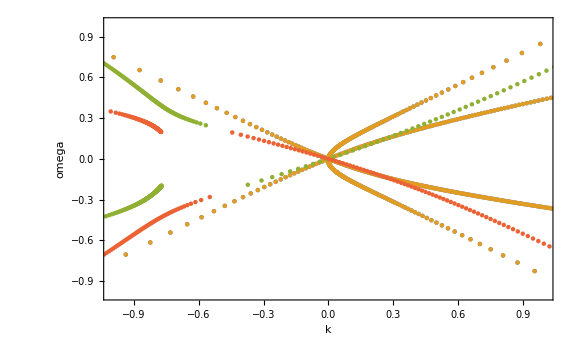

```mathematica
Show[%,PlotRange->{{-1,1},{-1,1}}]
```

??? Optical branch???

## More Beams

Divide beams

```mathematica
arcCosDivide[nDivide_]:=ArcCos@Table[0.8-n 0.8*2/nDivide,{n,0,nDivide}]
```

To solve the problem with more beams, I need to solve each step numerically.

```mathematica
nMatFun5Beams[g1_,g2_,g3_,g4_,g5_,g6_,nIndex_,theta1_,theta2_,theta3_,theta4_,theta5_,theta6_]=Module[{theta1M,theta2M,theta3M,theta4M,theta5M,theta6M,nMatM},
theta1M=theta1;
theta2M=theta2;
theta3M=theta3;
theta4M=theta4;
theta5M=theta5;
theta6M=theta6;


nMatM=(g1 nMatIntPhi0[theta1,nIndex]Sin[theta1]+g2 nMatIntPhi0[theta2,nIndex]Sin[theta2]+g3 nMatIntPhi0[theta3,nIndex]Sin[theta3]+g4 nMatIntPhi0[theta4,nIndex]Sin[theta4]+g5 nMatIntPhi0[theta5M,nIndex]Sin[theta5M]+g6 nMatIntPhi0[theta6M,nIndex]Sin[theta6M]);



nMatM[[1]]=-nMatM[[1]];

nMatM

];
```

```mathematica
nMatFunNBeams[gList_,nIndex_,thetaList_]:=Module[{thetaListM,nMatM,lengthM},
thetaListM=thetaList;
lengthM=Length@gList;

nMatM=Total@Table[gList[[i]] nMatIntPhi0[thetaListM[[i]],nIndex]Sin[ thetaListM[[i]] ],{i,1,lengthM}];

nMatM[[1]]=-nMatM[[1]];

nMatM

];
```

```mathematica
nMatFunNBeams[{1,1,1,1,1,1},0.2,{ArcCos@0.8,ArcCos[0.5],ArcCos@0.3,ArcCos[-0.3],ArcCos[-0.5],ArcCos[-0.8]}]
```

{{-30.7615,0.,0.,-1.75664},{0.,10.9891,0.,0.},{0.,0.,10.9891,0.},{1.75664,0.,0.,8.78322}}

```mathematica
Table[
Outer[Times,
Eigenvalues@nMatFunNBeams[{1,1,1,1,1,1,1},n,{ArcCos@0.8,ArcCos[0.5],ArcCos@0.3,Pi/2,ArcCos[-0.3],ArcCos[-0.5],ArcCos[-0.8]}],{n,1}
],
{n,-4,4,0.5}]
```

{{{-43.0474-20.6279 ⅈ,10.7619+5.15698 ⅈ},{-43.0474+20.6279 ⅈ,10.7619-5.15698 ⅈ},{43.0474+0. ⅈ,-10.7619+0. ⅈ},{43.0474+0. ⅈ,-10.7619+0. ⅈ}},{{-349.604,99.8868},{182.87,-52.2486},{182.87,-52.2486},{-16.1362,4.61033}},{{174.501,-58.1668},{-84.896,28.2987},{-84.896,28.2987},{-4.70851,1.5695}},{{19.7527-22.8564 ⅈ,-7.90106+9.14256 ⅈ},{19.7527+22.8564 ⅈ,-7.90106-9.14256 ⅈ},{-19.7527+0. ⅈ,7.90106+0. ⅈ},{-19.7527+0. ⅈ,7.90106+0. ⅈ}},{{-1.83794×10^16,9.1897×10^15},{9.1897×10^15,-4.59485×10^15},{9.1897×10^15,-4.59485×10^15},{-28.,14.}},{{41.9989,-27.9993},{-24.3368,16.2245},{-24.3368,16.2245},{6.67465,-4.44977}},{{50.0493,-50.0493},{-18.3467,18.3467},{-18.3467,18.3467},{-13.3559,13.3559}},{{19.3199,-38.6398},{-7.34514,14.6903},{-7.34514,14.6903},{-4.62963,9.25925}},{{0.,-36.6934},{0.,14.0341},{0.,14.0341},{0.,8.62507}},{{-19.3199,-38.6398},{7.34514,14.6903},{7.34514,14.6903},{4.62963,9.25925}},{{-50.0493,-50.0493},{18.3467,18.3467},{18.3467,18.3467},{13.3559,13.3559}},{{-41.9989,-27.9993},{24.3368,16.2245},{24.3368,16.2245},{-6.67465,-4.44977}},{{-3.67588×10^16,-1.83794×10^16},{1.83794×10^16,9.1897×10^15},{1.83794×10^16,9.1897×10^15},{32.,16.}},{{-19.7527+22.8564 ⅈ,-7.90106+9.14256 ⅈ},{-19.7527-22.8564 ⅈ,-7.90106-9.14256 ⅈ},{19.7527+0. ⅈ,7.90106+0. ⅈ},{19.7527+0. ⅈ,7.90106+0. ⅈ}},{{-174.501,-58.1668},{84.896,28.2987},{84.896,28.2987},{4.70851,1.5695}},{{349.604,99.8868},{-182.87,-52.2486},{-182.87,-52.2486},{16.1362,4.61033}},{{43.0474+20.6279 ⅈ,10.7619+5.15698 ⅈ},{43.0474-20.6279 ⅈ,10.7619-5.15698 ⅈ},{-43.0474+0. ⅈ,-10.7619+0. ⅈ},{-43.0474+0. ⅈ,-10.7619+0. ⅈ}}}

```mathematica
dataPltNBeamsPlt[gList_,thetaList_,numrange_:{-8.9,8.9},numstep_:0.09,pltRange_:{{-5,5},{-5,5}}]:=Module[{eigenDataM,pltDataM},

eigenDataM=Table[
Outer[Times,
Eigenvalues@nMatFunNBeams[gList,nM,thetaList],{nM,1}],
{nM,First@numrange,Last@numrange,numstep}];

pltDataM=eigenDataM;

ListPlot[pltDataM,Joined->False,Frame->True,ImageSize->Large,PlotRange->pltRange,FrameLabel->{"k","omega"}]

];
```

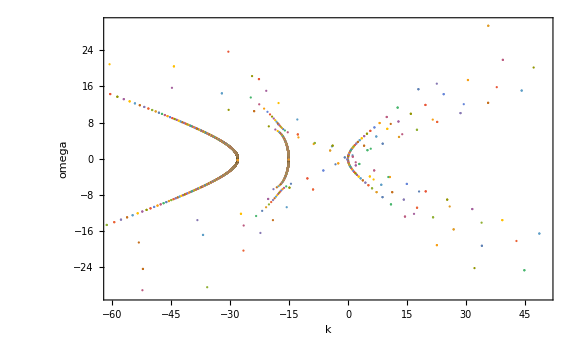

```mathematica
b6s0=dataPltNBeamsPlt[{1,1,1,-1,-1,-1},{ArcCos@0.8,ArcCos[0.5],ArcCos@0.3,ArcCos[-0.3],ArcCos[-0.5],ArcCos[-0.8]},{-101,101},0.049,{{-60,50},{-30,30}}]
```

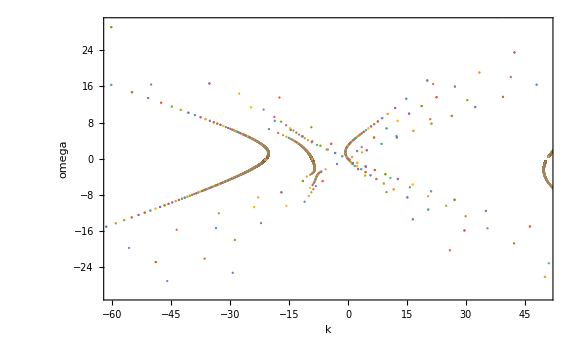

```mathematica
b6s1=dataPltNBeamsPlt[{1,1,1,-0.5,-0.5,-0.2},{ArcCos@0.8,ArcCos[0.5],ArcCos@0.3,ArcCos[-0.3],ArcCos[-0.5],ArcCos[-0.8]},{-101,101},0.049,{{-60,50},{-30,30}}]
```

```mathematica
dataPltNBeamsPlt[{0.5/(2Pi),0.5/(2Pi),-0.5/(2Pi),-0.5/(2Pi)},{ArcCos@0.8,ArcCos@0.3,ArcCos[-0.2],ArcCos[-0.8]},{-5,5},0.0049,{{-10,10},{-10,10}}]
```

```mathematica
dataPltNBeamsPlt[Join[Table[1,{i,1,5}],Table[-1,{i,1,5}]],arcCosDivide[10],{-101,101},0.049,{{-60,50},{-50,50}}]
```

-Graphics-

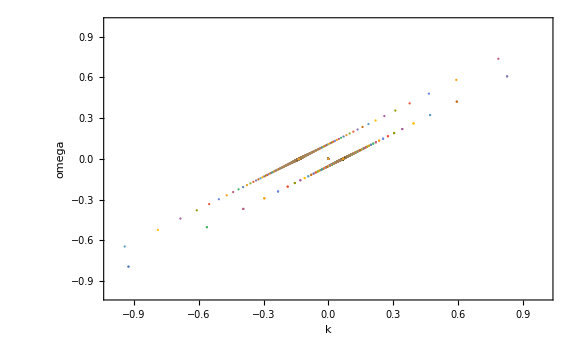

```mathematica
dataPltNBeamsPlt[{-0.5/(2Pi)},{ArcCos@0.8},{-101,101},0.049,{{-1,1},{-1,1}}]
```

## Continuous Distribution

```mathematica
gDistCont[g0_,ctheta_]:=g0 Piecewise[
{
{1,Pi/3≤ctheta≤Pi/2},
{-1,Pi/2<ctheta≤Pi/3+Pi/2}
}
]
```

```mathematica
nMatIntPhiCont[theta_,nIndex_,thetaK_:0,phiK_:0]:=Module[{thetaM,phiKM,thetaKM},

thetaM=theta;
phiKM=phiK;
thetaKM=thetaK;

Assuming[nIndex∈Reals && (-1<n<0||0<n<1),
Integrate[
vvMatrix[thetaM,phi]/(kno[nIndex,thetaKM,phiKM].eta.v[thetaM,phi]),
{phi,0,2Pi}]
]
];
```

```mathematica
nMatIntPhi0Cont[theta_,n_]=nMatIntPhiCont[theta,n,0,0]
```

{{(2 π)/(1-n Cos[theta]),0,0,(2 π Cos[theta])/(1-n Cos[theta])},{0,(π Sin[theta]^2)/(1-n Cos[theta]),0,0},{0,0,(π Sin[theta]^2)/(1-n Cos[theta]),0},{(2 π Cos[theta])/(1-n Cos[theta]),0,0,(2 π Cos[theta]^2)/(1-n Cos[theta])}}

```mathematica
nMatIntPhi0ContSimplified[ctheta_,n_]:={{(2 π)/(1-n ctheta),0,0,(2 π ctheta)/(1-n  ctheta)},{0,(π (1-ctheta^2))/(1-n ctheta),0,0},{0,0,(π (1-ctheta^2))/(1-n ctheta),0},{(2 π ctheta)/(1-n  ctheta),0,0,(2 π ctheta^2)/(1-n ctheta)}}
```

```mathematica
nMatIntPhiIntThetaCont[gL_,gR_,n_]=
Assuming[
n∈Reals && ctheta∈Reals&&(0<n<2||-2/(√3)<n<0),
Integrate[
gL nMatIntPhi0ContSimplified[ctheta,n],
{ctheta,0,Cos[Pi/3]}]+Integrate[
gR nMatIntPhi0ContSimplified[ctheta,n],
{ctheta,Cos[Pi/2+Pi/3],0}]
]
```

{{(2 gL π Log[-2/(-2+n)])/n+(2 gR π Log[1+(√3 n)/2])/n,0,0,(gL π (-n+Log[4]-2 Log[2-n]))/n^2-(gR π (√3 n+Log[4]-2 Log[2+√3 n]))/n^2},{0,-(gL π (-n (4+n)+8 (-1+n^2) Log[1-n/2]))/(8 n^3)+(gR π (4 √3 n-3 n^2+Log[256]-8 n^2 Log[2/(2+√3 n)]-8 Log[2+√3 n]))/(8 n^3),0,0},{0,0,-(gL π (-n (4+n)+8 (-1+n^2) Log[1-n/2]))/(8 n^3)+(gR π (4 √3 n-3 n^2+Log[256]-8 n^2 Log[2/(2+√3 n)]-8 Log[2+√3 n]))/(8 n^3),0},{(gL π (-n+Log[4]-2 Log[2-n]))/n^2-(gR π (√3 n+Log[4]-2 Log[2+√3 n]))/n^2,0,0,(gL π (-n (4+n)+Log[256/(-2+n)^8]))/(4 n^3)+(gR π (-4 √3 n+3 n^2-8 Log[2]+8 Log[2+√3 n]))/(4 n^3)}}

```mathematica
N@Det[
omega eta+nMatIntPhiIntThetaCont[1,-1,nIndex]
]
```

1/nIndex^5 0.25 (-1. omega-(0.392699 (-1. nIndex (4.+nIndex)+8. (-1.+nIndex^2) Log[1.-0.5 nIndex]))/nIndex^3-(0.392699 (5.54518+6.9282 nIndex-3. nIndex^2-8. nIndex^2 Log[2./(2.+1.73205 nIndex)]-8. Log[2.+1.73205 nIndex]))/nIndex^3)^2 (nIndex (nIndex omega-6.28319 Log[1.+0.866025 nIndex]+6.28319 Log[-2./(-2.+nIndex)]) (17.4207+9.19922 nIndex-12.5664 nIndex^2-4. nIndex^3 omega+3.14159 Log[256./(-2.+nIndex)^8]-25.1327 Log[2.+1.73205 nIndex])-4. nIndex (8.71034+2.29981 nIndex-6.28319 Log[2.-1. nIndex]-6.28319 Log[2.+1.73205 nIndex])^2)

```mathematica
omegaFunCont[nIndex_]=omega/.Solve[N@Det[
omega eta+nMatIntPhiIntThetaCont[1,-1,nIndex]
]==0,
omega]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{1/nIndex^3 1.65247×10^-23 (-1.31778×10^23-6.9587×10^22 nIndex+9.50576×10^22 nIndex^2+1.90115×10^23 Log[1.-0.5 nIndex]-1.90115×10^23 nIndex^2 Log[1.-0.5 nIndex]+1.90115×10^23 nIndex^2 Log[2./(2.+1.73205 nIndex)]+1.90115×10^23 Log[2.+1.73205 nIndex]),1/nIndex^3 1.65247×10^-23 (-1.31778×10^23-6.9587×10^22 nIndex+9.50576×10^22 nIndex^2+1.90115×10^23 Log[1.-0.5 nIndex]-1.90115×10^23 nIndex^2 Log[1.-0.5 nIndex]+1.90115×10^23 nIndex^2 Log[2./(2.+1.73205 nIndex)]+1.90115×10^23 Log[2.+1.73205 nIndex]),1/nIndex^4 6.00616×10^-61 (3.62559×10^60 nIndex+1.91454×10^60 nIndex^2-2.61531×10^60 nIndex^3+5.23062×10^60 nIndex^3 Log[1.+0.866025 nIndex]+6.53827×10^59 nIndex Log[256./(-2.+nIndex)^8]-5.23062×10^60 nIndex^3 Log[-2./(-2.+nIndex)]-5.23062×10^60 nIndex Log[2.+1.73205 nIndex]-1. √((-3.62559×10^60 nIndex-1.91454×10^60 nIndex^2+2.61531×10^60 nIndex^3-5.23062×10^60 nIndex^3 Log[1.+0.866025 nIndex]-6.53827×10^59 nIndex Log[256./(-2.+nIndex)^8]+5.23062×10^60 nIndex^3 Log[-2./(-2.+nIndex)]+5.23062×10^60 nIndex Log[2.+1.73205 nIndex])^2-3.32991×10^60 nIndex^4 (6.31602×10^61+3.33526×10^61 nIndex+4.40307×10^60 nIndex^2-9.11209×10^61 Log[2.-1. nIndex]-2.40588×10^61 nIndex Log[2.-1. nIndex]+3.28649×10^61 Log[2.-1. nIndex]^2+2.27802×10^61 Log[1.+0.866025 nIndex]+1.20294×10^61 nIndex Log[1.+0.866025 nIndex]-1.64325×10^61 nIndex^2 Log[1.+0.866025 nIndex]+4.10812×10^60 Log[1.+0.866025 nIndex] Log[256./(-2.+nIndex)^8]-2.27802×10^61 Log[-2./(-2.+nIndex)]-1.20294×10^61 nIndex Log[-2./(-2.+nIndex)]+1.64325×10^61 nIndex^2 Log[-2./(-2.+nIndex)]-4.10812×10^60 Log[256./(-2.+nIndex)^8] Log[-2./(-2.+nIndex)]-9.11209×10^61 Log[2.+1.73205 nIndex]-2.40588×10^61 nIndex Log[2.+1.73205 nIndex]+6.57299×10^61 Log[2.-1. nIndex] Log[2.+1.73205 nIndex]-3.28649×10^61 Log[1.+0.866025 nIndex] Log[2.+1.73205 nIndex]+3.28649×10^61 Log[-2./(-2.+nIndex)] Log[2.+1.73205 nIndex]+3.28649×10^61 Log[2.+1.73205 nIndex]^2))),1/nIndex^4 6.00616×10^-61 (3.62559×10^60 nIndex+1.91454×10^60 nIndex^2-2.61531×10^60 nIndex^3+5.23062×10^60 nIndex^3 Log[1.+0.866025 nIndex]+6.53827×10^59 nIndex Log[256./(-2.+nIndex)^8]-5.23062×10^60 nIndex^3 Log[-2./(-2.+nIndex)]-5.23062×10^60 nIndex Log[2.+1.73205 nIndex]+√((-3.62559×10^60 nIndex-1.91454×10^60 nIndex^2+2.61531×10^60 nIndex^3-5.23062×10^60 nIndex^3 Log[1.+0.866025 nIndex]-6.53827×10^59 nIndex Log[256./(-2.+nIndex)^8]+5.23062×10^60 nIndex^3 Log[-2./(-2.+nIndex)]+5.23062×10^60 nIndex Log[2.+1.73205 nIndex])^2-3.32991×10^60 nIndex^4 (6.31602×10^61+3.33526×10^61 nIndex+4.40307×10^60 nIndex^2-9.11209×10^61 Log[2.-1. nIndex]-2.40588×10^61 nIndex Log[2.-1. nIndex]+3.28649×10^61 Log[2.-1. nIndex]^2+2.27802×10^61 Log[1.+0.866025 nIndex]+1.20294×10^61 nIndex Log[1.+0.866025 nIndex]-1.64325×10^61 nIndex^2 Log[1.+0.866025 nIndex]+4.10812×10^60 Log[1.+0.866025 nIndex] Log[256./(-2.+nIndex)^8]-2.27802×10^61 Log[-2./(-2.+nIndex)]-1.20294×10^61 nIndex Log[-2./(-2.+nIndex)]+1.64325×10^61 nIndex^2 Log[-2./(-2.+nIndex)]-4.10812×10^60 Log[256./(-2.+nIndex)^8] Log[-2./(-2.+nIndex)]-9.11209×10^61 Log[2.+1.73205 nIndex]-2.40588×10^61 nIndex Log[2.+1.73205 nIndex]+6.57299×10^61 Log[2.-1. nIndex] Log[2.+1.73205 nIndex]-3.28649×10^61 Log[1.+0.866025 nIndex] Log[2.+1.73205 nIndex]+3.28649×10^61 Log[-2./(-2.+nIndex)] Log[2.+1.73205 nIndex]+3.28649×10^61 Log[2.+1.73205 nIndex]^2)))}

```mathematica
omegaFunCont[1.4]
```

{0.98581,0.98581,-0.98581-2.83073 ⅈ,-0.98581+2.83073 ⅈ}

```mathematica
dataPltTwoBeamPltCont[placeholder_,numrange_:{-8.9,8.9},numstep_:0.009,pltRange_:{{-5,5},{-5,5}}]:=Module[{pltDataM},

pltDataM=Table[
Table[
{n,1}omegaFunCont[n][[i]],
{n,numrange[[1]],numrange[[2]],numstep}
],
{i,1,4}];

(*Export["export/pltdata-continuous-beams.csv",pltDataM]*)

ListPlot[pltDataM,Joined->False,Frame->True,ImageSize->Large,PlotRange->pltRange,FrameLabel->{"k","omega"}]
];
```

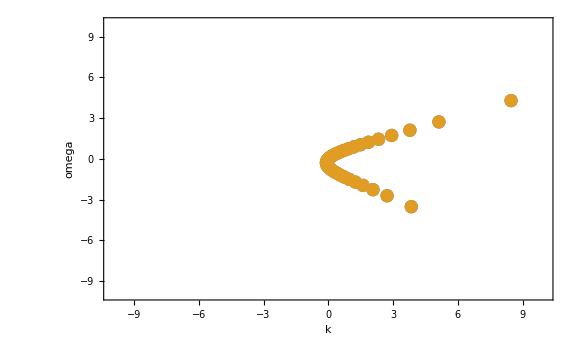

```mathematica
dataPltTwoBeamPltCont[1,{-100,100},0.09,{{-10,10},{-10,10}}]
```

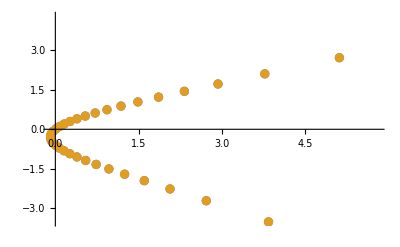

```mathematica
ListPlot@Table[
Table[
{n,1}omegaFunCont[n][[i]],
{n,-10,10,0.09}
],
{i,1,4}]
```

## Test

```mathematica
omegaFun[-0.5,0.5,n,ArcCos@0.9,ArcCos@0.3]-omegaFun[-0.5,0.5,-n,ArcCos@0.9,ArcCos@0.3]//FullSimplify
```

{0,0,0,0}

```mathematica
nMatIntPhi0[theta,n]//MatrixForm
```

((2 π)/(1-n Cos[theta]) | 0 | 0 | (2 π Cos[theta])/(1-n Cos[theta])
0 | (π Sin[theta]^2)/(1-n Cos[theta]) | 0 | 0
0 | 0 | (π Sin[theta]^2)/(1-n Cos[theta]) | 0
(2 π Cos[theta])/(1-n Cos[theta]) | 0 | 0 | (2 π Cos[theta]^2)/(1-n Cos[theta]))

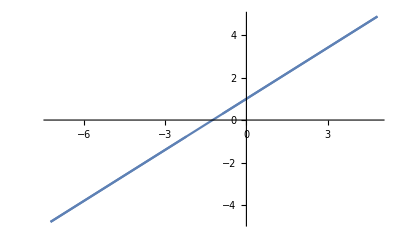

```mathematica
ListPlot[
Table[{nIndex 1/(1-0.8nIndex),1/(1-0.8nIndex)},{nIndex,-2.9,2.9,0.09}],
Joined->True]
```

```mathematica
Integrate[1/(1-n Cos@x),{x,0,Pi}]
```

```mathematica
Integrate[1/(1-nIndex Cos[phi] Cos[phiK]-nIndex Cos[theta] Cos[thetaK] Sin[phi] Sin[phiK]-nIndex Sin[phi] Sin[phiK] Sin[theta] Sin[thetaK]),{phi,0,2Pi}]
```

$Aborted

```mathematica
Integrate[1/(1-nIndex Cos[phi] Cos[phiK]-nIndex Cos[theta] Cos[thetaK] Sin[phi] Sin[phiK]-nIndex Sin[phi] Sin[phiK] Sin[theta] Sin[thetaK])/.{phiK->0,thetaK->0},{phi,0,2Pi}]
```

(2 √((1+nIndex)/(1-nIndex)) π)/(1+nIndex)

```mathematica
?FourierTransform
```

FourierTransform[expr,t,ω] gives the symbolic Fourier transform of expr. 
FourierTransform[expr,{t_1,t_2,…},{ω_1,ω_2,…}] gives the multidimensional Fourier transform of expr.

```mathematica
FourierTransform[1/(omega-kx vx-ky vy-kz vz),{omega,kx,ky,kz},{t,x,y,z}]
```

$Aborted

```mathematica
Outer[Times, {a1,a2,a3,a4},{b1,b2}]
```

{{a1 b1,a1 b2},{a2 b1,a2 b2},{a3 b1,a3 b2},{a4 b1,a4 b2}}

```mathematica
f[Sequence@@{a,b,c},Sequence@@{d,e,f}]
```

f[a,b,c,d,e,f]